# Violin String Model

## Miles Cochran-Branson, Claire Kvande, Fiona McLary, Sarah Powell

```mathematica
plotOpts = {Axes->{True,False},(*Show only the x-axis*)
		      AxesOrigin->{0,0},(*Set the origin to (0,0)*)
		      Frame->True,(*Enable frame around the plot*)
		      FrameTicks->{Automatic,Automatic},(*Show frame ticks for both axes*)
		      FrameStyle->Directive[Black,16],(*Style the frame labels*)
		      FrameTicksStyle->16,(*Style the frame ticks*)
		      PlotStyle->Blue,(*Set plot color*)
		      ImageSize->400,(*Set plot size*)
		      AspectRatio->1,(*Make the frame square*)
		      PlotRangePadding->{Scaled[0],Scaled[0.1]},(*Padding for better visibility*)
		      GridLines->Automatic (*Add grid lines for clarity*),
		      PlotLabel->Style["",18,Bold],BaseStyle->{FontFamily->"Arial",FontSize->14}};
SetDirectory[NotebookDirectory[]];
```

## Plucked String With Damping

First, we choose a suitable choice of parameters and define an applied force over a small period of time and space. This corresponds to plucking a string starting from t = 0 in a localized point.

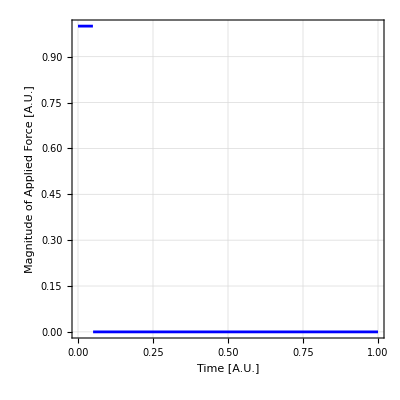

```mathematica
γ =0.2; (* damping term. We want this to be less than one for a real string *)
Fapplied = 1.0; (* magnitude of applied force *)
uPos = 0.1; (* possition along string of length 1 where pluck occurs*)
tPluck = 0; (* time at which pluck occurs *)
IntF[u_, t_] := If[(u > (uPos - 0.05) && u < (uPos + 0.05)) && (t > (tPluck - 0.05) && t < (tPluck +0.05)), Fapplied, 0]
plot = Plot[IntF[uPos, t], {t, 0, 1}, Evaluate@plotOpts,FrameLabel->{{"Magnitude of Applied Force [A.U.]",None},{"Time [A.U.]", None}}]
Export["plots/plucked_force.pdf", plot];
```

```mathematica
Directory[]
```

/Users/miles_cb

Then, we define the differential equation:

```mathematica
eqn = D[v[u, t],{t, 2}] + γ*D[v[u, t], t] - D[v[u, t], {u, 2}] - IntF[u, t] == 0;
soln = NDSolve[{eqn, v[0, t] == 0, v[1, t] == 0}, v[u, t], {u, 0, 1}, {t, 0, 20}]
```

{{v[u,t]→InterpolatingFunction[…][u,t]}}

and plot the solution:

```mathematica
plot =Plot3D[Evaluate[v[u, t] /. soln], {u, 0, 1}, {t, 0, 10}, AxesLabel->{"u", "t", "v"}, PlotRange->All]
Export["plots/plucked_solution_3d.pdf", plot];
```

-Graphics3D-

Finally, we can plot the shape of the string as a function of time:

```mathematica
Output[up_,tp_] := soln[[1]][[1]]/. t -> tp /. u -> up /. Rule[_,rhs_]:>rhs
Manipulate[Plot[Output[u, t], {u, 0, 1}, Evaluate@plotOpts, FrameLabel->{{"u [A.U.]",None},{"v [A.U.]", None}}, PlotRange->{-0.1, 0.1}], {t, 0.0, 20}]
```

```mathematica
gif = Table[Plot[Output[u, t], {u, 0, 1}, Evaluate@plotOpts, FrameLabel->{{"u [A.U.]",None},{"v [A.U.]", None}}, PlotRange->{-0.1, 0.1}], {t, 0.0, 20, 0.1}];
Export["plots/plucked_solution_vs_time.gif", gif];
```

## Simple Model of Bowed String

In order to model the bow, we apply a small force over multiple time steps

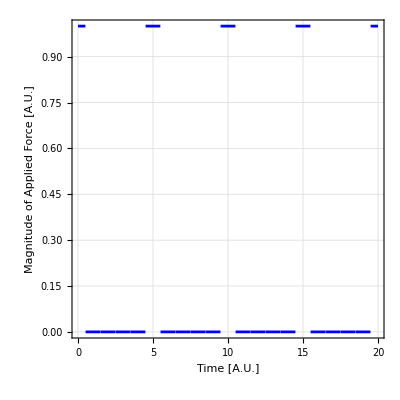

```mathematica
γ =0.1; (* lower damping to better see what's going on *)
IntF[u_, t_] := If[(u > (uPos - 0.05) && u < (uPos + 0.05)) && Mod[Round[t], 5] == 0, Fapplied, 0]
plot = Plot[IntF[uPos, t], {t, 0, 20}, Evaluate@plotOpts,FrameLabel->{{"Magnitude of Applied Force [A.U.]",None},{"Time [A.U.]", None}}]
Export["plots/bowed_force.pdf", plot];
```

```mathematica
eqn = D[v[u, t],{t, 2}] + γ*D[v[u, t], t] - D[v[u, t], {u, 2}] - IntF[u, t] == 0;
soln = NDSolve[{eqn, v[0, t] == 0, v[1, t] == 0}, v[u, t], {u, 0, 1}, {t, 0, 20}]
plot =Plot3D[Evaluate[v[u, t] /. soln], {u, 0, 1}, {t, 0, 10}, AxesLabel->{"u", "t", "v"}, PlotRange->All]
Export["plots/bowed_solution_3d.pdf", plot];
```

{{v[u,t]→InterpolatingFunction[…][u,t]}}

-Graphics3D-

```mathematica
Output[up_,tp_] := soln[[1]][[1]]/. t -> tp /. u -> up /. Rule[_,rhs_]:>rhs
Manipulate[Plot[Output[u, t], {u, 0, 1}, Evaluate@plotOpts, FrameLabel->{{"u [A.U.]",None},{"v [A.U.]", None}}, PlotRange->{-0.1, 0.1}], {t, 0.0, 20}]
```